```mathematica
SFColor={92,129,182}/256
MIColor={235,98,48}/256
QColor={225,156,38}/256
LColor={146,149,151}/256
green=CMYKColor[0.2883,0.055,0.4036,0]
pink=CMYKColor[0.0435,0.2683,0.2949,0]
blue=CMYKColor[0.355,0.1076,0.0982,0]
atomgreen= RGBColor[0.8, 1,0.2];
ColorData[97,"ColorList"]
QPLC=ColorData[94,"ColorList"]⟦1⟧
AtomColor=ColorData[97,"ColorList"]⟦3⟧
markerMI=Graphics[{RGBColor[MIColor],Disk[]}];
SetDirectory[NotebookDirectory[]]
<<MaTeX`
```

{23/64,129/256,91/128}

{235/256,49/128,3/16}

{225/256,39/64,19/128}

{73/128,149/256,151/256}

CMYKColor[0.2883, 0.055, 0.4036, 0]

CMYKColor[0.0435, 0.2683, 0.2949, 0]

CMYKColor[0.355, 0.1076, 0.0982, 0]

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

RGBColor[0.21020243862087418, 0.47802869583858715, 0.802198107305176]

RGBColor[0.560181, 0.691569, 0.194885]

Z:\Matthew\Figures\mbl_paper

```mathematica
ConfigureMaTeX["Ghostscript" -> FileNameJoin[{"C:","Program Files","gs","gs9.19","bin","gswin64c.exe"}]]
```

{pdfLaTeX→C:\Program Files (x86)\MiKTeX 2.9\miktex\bin\pdflatex.exe,CacheSize→100,Ghostscript→C:\Program Files\gs\gs9.19\bin\gswin64c.exe}

```mathematica
Gauss[x_,m_,s_]:=1/(√(2 π s^2))Exp[(-(x-m)^2)/(2 s^2)]
```

```mathematica
ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List: {Directive[GrayLevel[.3],Arrowheads[{{-0.05,0},{0.05,1}}]]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/.Line[x_,___]:>Arrow[x]
```

```mathematica
GenerateSpikeBall[loc_,radius_,disorderFrac_]:=Module[{Nspikes,ii,rvals,θvals,spikes,ctrlPtLists,allPts,peakOrValley,NctrlPts},
Nspikes=25;

NctrlPts=2Nspikes-1;
θvals=Subdivide[0,2π,NctrlPts-1];
For[ii=1,ii≤Length[θvals],ii++,
θvals⟦ii⟧=θvals⟦ii⟧+RandomReal[{-1,1}(2π)/NctrlPts disorderFrac/2];];
θvals=Sort[θvals];

rvals=ConstantArray[radius,{Length[θvals]}];
peakOrValley=1;
For[ii=1,ii≤Length[rvals],ii++,
randScalar=If[peakOrValley==1,
RandomReal[{Min[{1.2rvals⟦Mod[ii-1,NctrlPts,1]⟧,0.9radius}],radius(1+disorderFrac)}],
RandomReal[{radius(1-disorderFrac),Max[{0.8rvals⟦Mod[ii-1,NctrlPts,1]⟧,1.1radius}]}]];
rvals⟦ii⟧=rvals⟦ii⟧randScalar;
peakOrValley=Mod[peakOrValley+1,2];
];
θvals⟦-1⟧=θvals⟦1⟧;
rvals⟦-1⟧=rvals⟦1⟧;

allPts=Table[rvals⟦ii⟧{Cos[θvals⟦ii⟧],Sin[θvals⟦ii⟧]}+loc,{ii,1,Length[θvals]}];
ctrlPtLists=Table[allPts⟦Mod[ii+{0,1,2},NctrlPts,1]⟧,{ii,1,Length[θvals]-2,2}];
spikes=Table[BSplineCurve[ctrlPtLists⟦ii⟧],{ii,1,Length[ctrlPtLists]}];
Return[spikes];
];
```

```mathematica
ColorData[88,"ColorList"]
ColorData[89,"ColorList"]
{{ColorData[90,"ColorList"]}, {ColorData[91,"ColorList"]}}
ColorData[92,"ColorList"]
ColorData[93,"ColorList"]
ColorData[94,"ColorList"]
ColorData[95,"ColorList"]
ColorData[96,"ColorList"]
ColorData[97,"ColorList"]
```

{Hue[0.42, 0.67, 0.75],Hue[0.17, 1, 0.75],Hue[0.05, 0.7, 1],Hue[0.5, 0.67, 0.75],Hue[0.67, 0.5, 1],Hue[0.08, 1, 1],Hue[0.25, 0.67, 0.75],Hue[0.11, 0.75, 1],Hue[0.33, 0.33, 0.75],Hue[0.11, 1, 0.9]}

{Hue[0.5, 0.5, 0.4],Hue[0.08, 0.9, 0.8],Hue[0.42, 0.67, 0.6],Hue[0.13, 0.8, 0.85],Hue[0.5, 0.67, 0.6],Hue[0.17, 0.9, 0.6],Hue[0.67, 0.5, 0.7],Hue[0.1, 0.75, 0.8],Hue[0, 0.75, 0.8],Hue[0.04, 0.8, 1]}

{{{Hue[0.22, 1, 0.6],Hue[0.01, 0.8, 0.8],Hue[0.61, 0.75, 1],Hue[0.11, 1, 0.75],Hue[0.67, 0.6, 0.9],Hue[0.17, 1, 0.5],Hue[0.06, 1, 0.75],Hue[0.8, 0.5, 0.6],Hue[0.25, 1, 0.5],Hue[0.58, 0.67, 0.75]}},{{Hue[0.58, 0.67, 0.66],Hue[0.17, 1, 0.66],Hue[0.45, 0.75, 0.6],Hue[0.12, 0.7, 0.7],Hue[0.25, 0.7, 0.6],Hue[0.58, 0.5, 0.8],Hue[0.11, 1, 0.66],Hue[0.06, 0.75, 0.88],Hue[0.5, 0.5, 0.44],Hue[0.67, 0.33, 0.66]}}}

{Hue[0.12, 1, 0.9],Hue[0.08, 1, 0.7],Hue[0.08, 1, 0.92],Hue[0.17, 1, 0.5],Hue[0.12, 0.7, 0.8],Hue[0, 0.33, 0.6],Hue[0.11, 1, 0.8],Hue[0.5, 0.5, 0.5],Hue[0.17, 1, 0.7],Hue[0.06, 1, 0.69]}

{Hue[0, 0.8, 0.85],Hue[0.11, 0.75, 0.92],Hue[0.17, 0.6, 0.52],Hue[0.06, 0.75, 0.92],Hue[0.5, 0.5, 0.55],Hue[0.17, 0.67, 0.69],Hue[0.67, 0.33, 0.69],Hue[0.5, 0.33, 0.69],Hue[0.94, 0.5, 0.69],Hue[0.25, 0.6, 0.7]}

{RGBColor[0.21020243862087418, 0.47802869583858715, 0.802198107305176],RGBColor[0.7072726887298498, 0.36734389310000776, 0.22572660836392477],RGBColor[0., 0.5478609782372904, 0.4891696614045123],RGBColor[0.6451793884320347, 0.3592839366958893, 0.6737368466913262],RGBColor[0.4795214457262614, 0.4794496852752767, 0.08944520674023174],RGBColor[0., 0.5239638039480364, 0.7467101989958554],RGBColor[0.7618211845684226, 0.3099312712025551, 0.39120711213803705],RGBColor[0., 0.5380756485327808, 0.3011937398484862],RGBColor[0.4306391086785686, 0.4367088653451986, 0.7829127834334554],RGBColor[0.636471896284624, 0.413870747850409, 0.1431778775285077],RGBColor[0., 0.545007293737855, 0.6028975638566113],RGBColor[0.722244276284985, 0.31998937783312603, 0.5726766768035847],RGBColor[0.35984212281381656, 0.5088638151315594, 0.14452408433947048],RGBColor[0., 0.4987546431531366, 0.7933744520922773],RGBColor[0.7379047109639936, 0.34055347063409547, 0.2850977041876611]}

{RGBColor[0.5477407734491414, 0.6781411651751702, 0.9198755683649779],RGBColor[0.87058837853668, 0.6048248459110492, 0.4922838688297661],RGBColor[0.31573973298228514, 0.7398396909727576, 0.6872935044932373],RGBColor[0.8116530610702385, 0.6012280787481186, 0.8258505440142531],RGBColor[0.6930177876644076, 0.6799721277526325, 0.4199343626084721],RGBColor[0.3657383773643357, 0.7160575963243984, 0.8785934977977451],RGBColor[0.9085681481061203, 0.5752950706176673, 0.6133049627289092],RGBColor[0.45090413446768524, 0.7307307156470545, 0.5496494250722427],RGBColor[0.6615631128722788, 0.6485376038586634, 0.9060767343018842],RGBColor[0.8161522125541179, 0.6330873483332724, 0.44162556936219965],RGBColor[0.2788463407977611, 0.7364662593350805, 0.7719277055909679],RGBColor[0.872285951379566, 0.5806850315835889, 0.7504553721898173],RGBColor[0.6034618967403447, 0.7041963165762994, 0.44827550563732105],RGBColor[0.475063788418671, 0.6944493828400345, 0.9131877670467264],RGBColor[0.8931418160634189, 0.5902914113092578, 0.534183346558588]}

{RGBColor[0.23792049598428056, 0.6887478786077664, 1.],RGBColor[1., 0.519591857134656, 0.3096724501821112],RGBColor[0., 0.7904150911428401, 0.7051174286912738],RGBColor[0.9363550506359628, 0.5065315445234129, 0.9811070357073114],RGBColor[0.686958812227552, 0.6905735387590792, 0.05772651708573071],RGBColor[0., 0.7563606470844539, 1.],RGBColor[1., 0.42721725970620367, 0.5588721269654955],RGBColor[0., 0.7762699669879868, 0.4226781993994135],RGBColor[0.6109120054767144, 0.6265300918182286, 1.],RGBColor[0.9205702487735915, 0.5917459414248752, 0.1760364705511712],RGBColor[0., 0.7864948250314334, 0.8753587584942155],RGBColor[1., 0.4434532437298291, 0.8298247530580691],RGBColor[0.5070558429142891, 0.7339027322149217, 0.17362470759792137],RGBColor[0., 0.7194858914960536, 1.],RGBColor[1., 0.4770567658488352, 0.3999994395810451]}

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
Graphics[{GenerateSpikeBall[{0,0},0.55,0.85],GenerateSpikeBall[{2,0},0.75,0.25],GenerateSpikeBall[{4,0},0.75,0.1]}]
```

-Graphics-

{0,0}

{0,-0.5}

```mathematica
atomR=0.10;
atomShdwR=0.13;
```

{0,0}

{0,-0.5}

{0,0}

{0,-0.5}

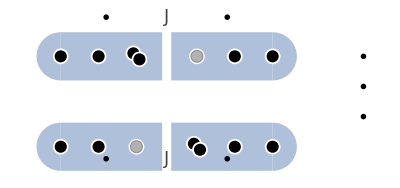
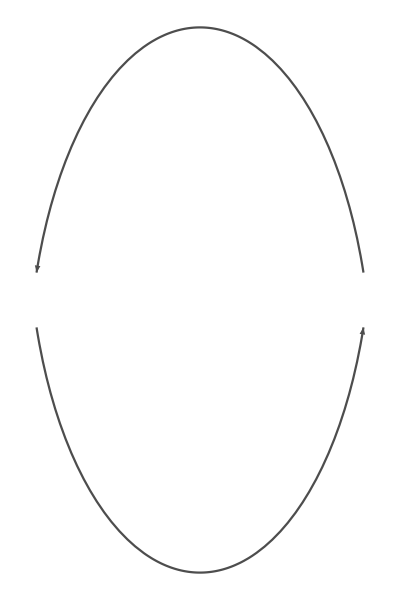

nf_ent_pills.pdf

{0,0}

{0,-1.5}

```mathematica
PillTxy={0,0}
PillBxy={0,-0.5}
BackGrndBox=Graphics[{
Blend[{ColorData[97,"ColorList"]⟦1⟧,RGBColor["White"]},0.5],
{Rectangle[{PillTxy⟦1⟧-1.75,PillTxy⟦2⟧-0.4},{PillTxy⟦1⟧-0.075,PillTxy⟦2⟧+0.4}]},
{Disk[{PillTxy⟦1⟧-1.75,PillTxy⟦2⟧},0.4,{π/2,3π/2}]},
{Rectangle[{PillTxy⟦1⟧+0.075,PillTxy⟦2⟧-0.4},{1.75,0.4}]},
{Disk[{PillTxy⟦1⟧+1.75,0},PillTxy⟦2⟧+0.4,{-π/2,π/2}]}
}];
N2Atoms=Graphics[{ 
RGBColor["Black"],
{Disk[{PillTxy⟦1⟧-1.75,PillTxy⟦2⟧},{atomR,atomR}]},
{Disk[{PillTxy⟦1⟧-1.125,PillTxy⟦2⟧},{atomR,atomR}]},
{Disk[{PillTxy⟦1⟧-0.5-0.05,PillTxy⟦2⟧+0.05},{atomR,atomR}]},
{Disk[{PillTxy⟦1⟧-0.5+0.05,PillTxy⟦2⟧-0.05},{atomR,atomR}]},
{Disk[{PillTxy⟦1⟧+1.125,PillTxy⟦2⟧},{atomR,atomR}]},
{Disk[{PillTxy⟦1⟧+1.75,PillTxy⟦2⟧},{atomR,atomR}]}
}];
N2Atoms2=Graphics[{ 
RGBColor["Black"],
{Disk[{PillTxy⟦1⟧-0.5+0.05,PillTxy⟦2⟧-0.05},{atomR,atomR}]}
}];
N2AtomsShadows=Graphics[{ 
RGBColor["White"],
{Opacity[1],Disk[{PillTxy⟦1⟧-1.75,PillTxy⟦2⟧},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{PillTxy⟦1⟧-1.125,PillTxy⟦2⟧},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{PillTxy⟦1⟧-0.5-0.05,PillTxy⟦2⟧+0.05},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{PillTxy⟦1⟧+1.125,PillTxy⟦2⟧},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{PillTxy⟦1⟧+1.75,PillTxy⟦2⟧},{atomShdwR,atomShdwR}]}
}];
N2AtomsShadows2=Graphics[{ 
RGBColor["White"],
{Opacity[1],Disk[{PillTxy⟦1⟧-0.5+0.05,PillTxy⟦2⟧-0.05},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{PillTxy⟦1⟧+0.5,PillTxy⟦2⟧},{atomShdwR,atomShdwR}]}
}];
rdsAndAnglsFlat={{0.1,{0.1 π,π 0.9}}};
arcsHopFlat= Graphics[{
Inset[arcsWArrows[rdsAndAnglsFlat],{PillTxy⟦1⟧,PillTxy⟦2⟧+0.3}]
}];
AtomHopped=Graphics[{
RGBColor["Black"],
Opacity[0.3],
EdgeForm[Dashing[0.005]],
Disk[{PillTxy⟦1⟧+0.5,PillTxy⟦2⟧},{atomR,atomR}]
}];




BackGrndBoxBot=Graphics[{
Blend[{ColorData[97,"ColorList"]⟦1⟧,RGBColor["White"]},0.5],
{Rectangle[{-1.75,PillBxy⟦2⟧-0.4-1},{-0.075,PillBxy⟦2⟧+0.4-1}]},
{Disk[{-1.75,PillBxy⟦2⟧+0-1},0.4,{π/2,3π/2}]},
{Rectangle[{0.075,PillBxy⟦2⟧-0.4-1},{1.75,PillBxy⟦2⟧+0.4-1}]},
{Disk[{1.75,PillBxy⟦2⟧+0-1},0.4,{-π/2,π/2}]}
}];
N2AtomsBot=Graphics[{ 
RGBColor["Black"],
{Disk[{PillBxy⟦1⟧-1.75,PillBxy⟦2⟧-1},{atomR,atomR}]},
{Disk[{PillBxy⟦1⟧-1.125,PillBxy⟦2⟧-1},{atomR,atomR}]},
{Disk[{PillBxy⟦1⟧+0.5-0.05,PillBxy⟦2⟧-1+0.05},{atomR,atomR}]},
{Disk[{PillBxy⟦1⟧+1.125,PillBxy⟦2⟧-1},{atomR,atomR}]},
{Disk[{PillBxy⟦1⟧+1.75,PillBxy⟦2⟧-1},{atomR,atomR}]}
}];
N2Atoms2Bot=Graphics[{ 
RGBColor["Black"],
{Disk[{PillBxy⟦1⟧+0.5+0.05,PillBxy⟦2⟧-0.05-1},{atomR,atomR}]}
}];
N2AtomsShadowsBot=Graphics[{ 
RGBColor["White"],
{Opacity[1],Disk[{PillBxy⟦1⟧-1.75,PillBxy⟦2⟧-1},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{PillBxy⟦1⟧-1.125,PillBxy⟦2⟧-1},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{PillBxy⟦1⟧+0.5-0.05,PillBxy⟦2⟧-1+0.05},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{PillBxy⟦1⟧+1.125,PillBxy⟦2⟧-1},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{PillBxy⟦1⟧+1.75,PillBxy⟦2⟧-1},{atomShdwR,atomShdwR}]}
}];
N2AtomsShadows2Bot=Graphics[{ 
RGBColor["White"],
{Opacity[1],Disk[{PillBxy⟦1⟧+0.5+0.05,PillBxy⟦2⟧-0.05-1},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{PillBxy⟦1⟧-0.5,PillBxy⟦2⟧-1},{atomShdwR,atomShdwR}]}
}];
rdsAndAnglsFlatBot2={{0.1,{0.1 π+π,π 0.9+π}}};
arcsHopFlatBot= Graphics[{
Inset[arcsWArrows[rdsAndAnglsFlatBot2],{PillBxy⟦1⟧,PillBxy⟦2⟧-1-0.3}]
}];
AtomHoppedBot=Graphics[{
RGBColor["Black"],
Opacity[0.3],
EdgeForm[Dashing[0.005]],
Disk[{PillBxy⟦1⟧-0.5,PillBxy⟦2⟧-1},{atomR,atomR}]
}];

FntSz=18;
Pilllabels={Graphics[{
{Opacity[0.75],Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{PillTxy⟦1⟧,PillTxy⟦2⟧0.5},{0,-1}]},
{Opacity[0.75],Text[Style[ToExpression["J",TeXForm,HoldForm],FntSz],{PillBxy⟦1⟧,PillBxy⟦2⟧-1.75-0.1},{0,-1}]}
}]};
PillLabels2=Graphics[{
Inset[MaTeX["\\mathbf |\\mathrm{N_A=4} \\mathbf \\rangle",Magnification->1.8],{-1,PillTxy⟦2⟧+0.5+0.15}],
Inset[MaTeX["\\mathbf | \\mathrm{N_B=2} \\mathbf \\rangle",Magnification->1.8],{1,PillTxy⟦2⟧+0.5+0.15}],
Inset[MaTeX["\\mathbf | \\mathrm{N_A=2} \\mathbf \\rangle",Magnification->1.8],{-1,PillBxy⟦2⟧-1.75+0.05}],
Inset[MaTeX["\\mathbf | \\mathrm{N_B=4} \\mathbf \\rangle",Magnification->1.8],{1,PillBxy⟦2⟧-1.75+0.05}],
Inset[MaTeX["\\mathbf | 4,2 \\mathbf \\rangle",Magnification->1.8],{3.25,PillTxy⟦2⟧}],
Inset[MaTeX["+",Magnification->1.8],{3.25,-0.5}],
Inset[MaTeX["\\mathbf | 2,4 \\mathbf \\rangle",Magnification->1.8],{3.25,PillBxy⟦2⟧-1}]

}];

Show[BackGrndBox,N2AtomsShadows,N2Atoms,
N2AtomsShadows2,N2Atoms2,
AtomHopped,arcsHopFlat,
BackGrndBoxBot,N2AtomsShadowsBot,N2AtomsBot,
N2AtomsShadows2Bot,N2Atoms2Bot,
arcsHopFlatBot,AtomHoppedBot,
Pilllabels,
PillLabels2]
Export["nf_ent_pills.pdf",%,Rasterize-> False,ImageResolution-> 1000]
```

{0,0}

{0,-1.5}

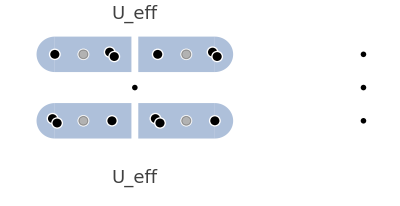
-Graphics-
-Graphics-

```mathematica
PillTxy={0,0}
PillBxy={0,-1.5}
BackGrndBox=Graphics[{
Blend[{ColorData[97,"ColorList"]⟦1⟧,RGBColor["White"]},0.5],
{Rectangle[{-1.75  + PillTxy⟦1⟧,-0.4 + PillTxy⟦2⟧},{-0.075 + PillTxy⟦1⟧,0.4 + PillTxy⟦2⟧}]},
{Disk[{-1.75 + PillTxy⟦1⟧,0 + PillTxy⟦2⟧},0.4,{π/2,3π/2}]},
{Rectangle[{0.075 + PillTxy⟦1⟧ ,-0.4 + PillTxy⟦2⟧},{1.75,0.4}]},
{Disk[{1.75 + PillTxy⟦1⟧,0 + PillTxy⟦2⟧},0.4,{-π/2,π/2}]}
}];
N2AtomsTop=Graphics[{ 
RGBColor["Black"],
{Disk[{1.75-0.05 + PillTxy⟦1⟧,0.05+ PillTxy⟦2⟧},{atomR,atomR}]},
{Disk[{-0.5-0.05 + PillTxy⟦1⟧,+0.05 +  PillTxy⟦2⟧},{atomR,atomR}]},
{Disk[{-1.75 + PillTxy⟦1⟧,0 +  PillTxy⟦2⟧},{atomR,atomR}]},
{Disk[{0.5 + PillTxy⟦1⟧,0 +  PillTxy⟦2⟧},{atomR,atomR}]}
}];
N2Atoms2Top=Graphics[{ 
RGBColor["Black"],
{Disk[{-0.5+0.05,-0.05 +  PillTxy⟦2⟧},{atomR,atomR}]},
{Disk[{1.75+0.05,-0.05 +  PillTxy⟦2⟧},{atomR,atomR}]}
}];
N2AtomsShadowsTop=Graphics[{ 
RGBColor["White"],
{Opacity[1],Disk[{1.75-0.05 +  PillTxy⟦1⟧,0.05 +  PillTxy⟦2⟧},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{1.125 +  PillTxy⟦1⟧,0 +  PillTxy⟦2⟧},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-0.5-0.05 + PillTxy⟦1⟧,0.05 +  PillTxy⟦2⟧},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{0.5 + PillTxy⟦1⟧,0 +  PillTxy⟦2⟧},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-1.125 + PillTxy⟦1⟧,0 +  PillTxy⟦2⟧},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-1.75 + PillTxy⟦1⟧,0 +  PillTxy⟦2⟧},{atomShdwR,atomShdwR}]}
}];
N2AtomsShadows2Top=Graphics[{ 
RGBColor["White"],
{Opacity[1],Disk[{-0.5+0.05 + PillTxy⟦1⟧,-0.05 + PillTxy⟦2⟧},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{1.75+0.05 + PillTxy⟦1⟧,-0.05 +  PillTxy⟦2⟧},{atomShdwR,atomShdwR}]}
}];
rdsAndAnglsFlat={{0.1,{0.1 π,π 0.9}}};
arcsHopFlat= Graphics[{
Inset[arcsWArrows[rdsAndAnglsFlat],{0 + PillTxy⟦1⟧,0.3 + PillTxy⟦2⟧}]
}];
AtomHoppedTop=Graphics[{
RGBColor["Black"],
Opacity[0.3],
EdgeForm[Dashing[0.005]],
Disk[{-1.125 + PillTxy⟦1⟧,0 + PillTxy⟦2⟧},{atomR,atomR}],
Disk[{1.125 + PillTxy⟦1⟧,0 + PillTxy⟦2⟧},{atomR,atomR}]
}];



BackGrndBoxBot=Graphics[{
Blend[{ColorData[97,"ColorList"]⟦1⟧,RGBColor["White"]},0.5],
{Rectangle[{-1.75 + PillBxy⟦1⟧,-0.4 +  PillBxy⟦2⟧},{-0.075 + PillBxy⟦1⟧,0.4 + PillBxy⟦2⟧}]},
{Disk[{-1.75 + PillBxy⟦1⟧,0 + PillBxy⟦2⟧},0.4,{π/2,3π/2}]},
{Rectangle[{0.075 + PillBxy⟦1⟧,-0.4 + PillBxy⟦2⟧},{1.75 + PillBxy⟦1⟧,0.4 + PillBxy⟦2 ⟧}]},
{Disk[{1.75 + PillBxy⟦1⟧,0 + PillBxy⟦2⟧},0.4,{-π/2,π/2}]}
}];
N2AtomsBot=Graphics[{ 
RGBColor["Black"],
{Disk[{-1.75-0.05 + PillBxy⟦1⟧,0.05 +  PillBxy⟦2⟧},{atomR,atomR}]},
{Disk[{0.5-0.05 + PillBxy⟦1⟧,0.05 +  PillBxy⟦2⟧},{atomR,atomR}]},
{Disk[{1.75 + PillBxy⟦1⟧,0 +  PillBxy⟦2⟧},{atomR,atomR}]},
{Disk[{-0.5 + PillBxy⟦1⟧,0 +  PillBxy⟦2⟧},{atomR,atomR}]}
}];
N2Atoms2Bot=Graphics[{ 
RGBColor["Black"],
{Disk[{0.5+0.05 + PillBxy⟦1⟧,-0.05 +  PillBxy⟦2⟧},{atomR,atomR}]},
{Disk[{-1.75+0.05 + PillBxy⟦1⟧,-0.05 +  PillBxy⟦2⟧},{atomR,atomR}]}
}];
N2AtomsShadowsBot=Graphics[{ 
RGBColor["White"],
{Opacity[1],Disk[{-1.75-0.05 + PillBxy⟦1⟧,0.05 +  PillBxy⟦2⟧},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-1.125 + PillBxy⟦1⟧,0 +  PillBxy⟦2⟧},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{0.5-0.05 + PillBxy⟦1⟧,0.05 +  PillBxy⟦2⟧},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-0.5 + PillBxy⟦1⟧, PillBxy⟦2⟧},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{1.125 + PillBxy⟦1⟧,0 +  PillBxy⟦2⟧},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{1.75 + PillBxy⟦1⟧,0 +  PillBxy⟦2⟧},{atomShdwR,atomShdwR}]}
}];
N2AtomsShadows2Bot=Graphics[{ 
RGBColor["White"],
{Opacity[1],Disk[{0.5+0.05 + PillBxy⟦1⟧,-0.05 +  PillBxy⟦2⟧},{atomShdwR,atomShdwR}]},
{Opacity[1],Disk[{-1.75+0.05 + PillBxy⟦1⟧,-0.05 +  PillBxy⟦2⟧},{atomShdwR,atomShdwR}]}
}];
rdsAndAnglsFlatBot2={{0.1,{0.1 π+π,π 0.9+π}}};
arcsHopFlatBot= Graphics[{
Inset[arcsWArrows[rdsAndAnglsFlatBot2],{ PillBxy⟦1⟧,PillBxy⟦2⟧-0.3}]
}];
AtomHoppedBot=Graphics[{
RGBColor["Black"],
Opacity[0.3],
EdgeForm[Dashing[0.005]],
Disk[{-1.125 + PillBxy⟦1⟧,0 + PillBxy⟦2⟧},{atomR,atomR}],
Disk[{1.125 + PillBxy⟦1⟧,0 + PillBxy⟦2⟧},{atomR,atomR}]
}];


ketX=5;
FntSz=18;
MatexMag=1.8;
Pilllabels={Graphics[{
{Opacity[0.75],Text[Style[ToExpression["U_{eff}",TeXForm,HoldForm],FntSz],{0,0.7},{0,PillBxy⟦2⟧}]},
{Opacity[0.75],Text[Style[ToExpression["U_{eff}",TeXForm,HoldForm],FntSz],{0,PillBxy⟦2⟧+-1.5},{0,PillBxy⟦2⟧}]}
}]};
PillLabels2=Graphics[{
Inset[MaTeX["\\mathbf | 1,0,2 \\rangle \\otimes | 1,0,2 \\mathbf \\rangle",Magnification->MatexMag],{ketX,0+PillBxy⟦1⟧}],
Inset[MaTeX["+",Magnification->MatexMag],{ketX, (PillBxy⟦2⟧+ PillTxy⟦2⟧)/2}],
Inset[MaTeX["+",Magnification->MatexMag],{0, (PillBxy⟦2⟧+ PillTxy⟦2⟧)/2}],
Inset[MaTeX["\\mathbf | 2,0,1 \\rangle \\otimes | 2,0,1 \\mathbf \\rangle",Magnification->MatexMag],{ketX,0+PillBxy⟦2⟧}]
}];

Show[BackGrndBox,N2AtomsShadowsTop,N2AtomsTop,
N2AtomsShadows2Top,N2Atoms2Top,
AtomHoppedTop,arcsHopFlat,
BackGrndBoxBot,N2AtomsShadowsBot,N2AtomsBot,
N2AtomsShadows2Bot,N2Atoms2Bot,
arcsHopFlatBot,AtomHoppedBot,
Pilllabels,
PillLabels2]
(*Export["np_ent_pills.pdf",%,Rasterize-> False,ImageResolution-> 1000]*)
```